# QuantumCircuit Usage Examples

Elementary usagepaclet:Q3/tutorial/QuantumCircuitUsage#1868432623 | Examples with Measurementspaclet:Q3/tutorial/QuantumCircuitUsage#1921589536
Grouping Circuit Elements With { }paclet:Q3/tutorial/QuantumCircuitUsage#188399535 | Examples with Controlled-U Gatespaclet:Q3/tutorial/QuantumCircuitUsage#580366830
Automatic Conversion to Operator Expressionspaclet:Q3/tutorial/QuantumCircuitUsage#729173090 | Examples with Arbitrary Controlled-U Gatespaclet:Q3/tutorial/QuantumCircuitUsage#87721419
More Complicated Gatespaclet:Q3/tutorial/QuantumCircuitUsage#2136908654 | Matrix on QuantumCircuitpaclet:Q3/tutorial/QuantumCircuitUsage#462801707
With Inputs and Outputspaclet:Q3/tutorial/QuantumCircuitUsage#94058740 | Matrix on QuantumCircuit: With Measurepaclet:Q3/tutorial/QuantumCircuitUsage#991141748
Example with GraphStatespaclet:Q3/tutorial/QuantumCircuitUsage#175892259 |

QuantumCircuitpaclet:Q3/ref/QuantumCircuitQ3 Package Symbol provides the graphical representation of the quantum circuits.

QuantumCircuitpaclet:Q3/ref/QuantumCircuitQ3 Package Symbol | Graphical representation of quantum circuit
Phasepaclet:Q3/ref/PhaseQ3 Package Symbol | Single-qubit phase gate (relative phase)
Rotationpaclet:Q3/ref/RotationQ3 Package Symbol | Single-qubit rotation gate
EulerRotationpaclet:Q3/ref/EulerRotationQ3 Package Symbol | Single-qubit rotation gate specified by Euler angles
CNOTpaclet:Q3/ref/CNOTQ3 Package Symbol | Two-qubit controlled NOT gate
CZpaclet:Q3/ref/CZQ3 Package Symbol | Two-qubit controlled Z gate
SWAPpaclet:Q3/ref/SWAPQ3 Package Symbol | Two-qubit SWAP gate
Toffolipaclet:Q3/ref/ToffoliQ3 Package Symbol | Three-qubit Toffoli gate
ControlledUpaclet:Q3/ref/ControlledUQ3 Package Symbol | Multi-qubit controlled-U gate

Elements in the quantum circuit representation.

## Elementary usage

First load the application (the collection of packages).

```mathematica
<<Q3`
```

QuantumCircuitpaclet:Q3/ref/QuantumCircuitQ3 Package Symbol works for labeled qubits.

```mathematica
Let[Qubit,S]
```

QuantumCircuitpaclet:Q3/ref/QuantumCircuitQ3 Package Symbol is a collection of quantum logic gates. Usually, it is displayed in a graphical form.

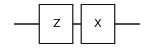

```mathematica
QuantumCircuit[S[1,3],S[1,1]]
```

Graphics directives can be used to change the style of labels of the quantum logic gates.

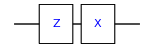

```mathematica
QuantumCircuit[Blue,S[1,3],S[1,1]]
```

0_S_10_S_2

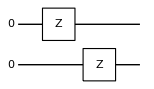

```mathematica
vec=LogicalForm[Ket[],S@{1,2}]
QuantumCircuit[vec,S[1,3],S[2,3]]
```

Here are all single-qubit gates displayed in a quantum circuit model.

```mathematica
QuantumCircuit[{S[1,1],S[2,2],S[3,3],S[4,6],S[5,7],S[6,8]},Null]
```

-Graphics-

“Spacer” is a special form to represent a time slice for no operation. It is useful for graphically extend certain time span. “Separator” puts a vertical dotted line to indicate a particular time slice.

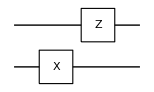

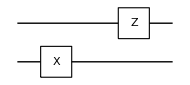

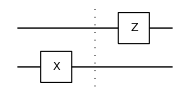

```mathematica
QuantumCircuit[S[2,1],S[1,3]]
QuantumCircuit[S[2,1],"Spacer",S[1,3]]
QuantumCircuit[S[2,1],"Separator",S[1,3]]
```

ExpressionForpaclet:Q3/ref/ExpressionForQ3 Package Symbol or Elaboratepaclet:Q3/ref/ElaborateQ3 Package Symbol converts QuantumCircuitpaclet:Q3/ref/QuantumCircuitQ3 Package Symbol to usual operator expressions in terms of the Pauli operators.

```mathematica
qc=QuantumCircuit[Blue, CNOT[S[1],S[2]]]
ExpressionFor[qc]
Elaborate[qc]
```

-Graphics-

1/2-1/2 S_1^z S_2^x+S_1^z/2+S_2^x/2

1/2-1/2 S_1^z S_2^x+S_1^z/2+S_2^x/2

Here is another example.

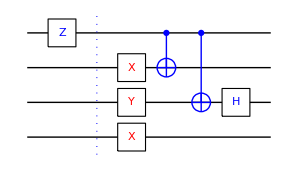

```mathematica
qc=QuantumCircuit[
Blue,S[1,3],"Separator",
{Red,S[2,1],S[3,2],S[4,1]},
{Blue, CNOT[S[1],S[2]] },
 CNOT[S[1],S[3]],
S[3,6]]
```

```mathematica
op=S[3,6]**CNOT[S[1],S[3]]**CNOT[S[1],S[2]]**S[4,1]**S[3,2]**S[2,1]**S[1,3]//Garner
```

(ⅈ S_1^z S_4^x)/(2 √2)-(S_3^y S_4^x)/(2 √2)+(S_1^z S_3^y S_4^x)/(2 √2)-(ⅈ S_2^x S_3^x S_4^x)/(2 √2)+(ⅈ S_2^x S_3^z S_4^x)/(2 √2)-(ⅈ S_1^z S_2^x S_3^x S_4^x)/(2 √2)+(ⅈ S_1^z S_2^x S_3^z S_4^x)/(2 √2)-(ⅈ S_4^x)/(2 √2)

```mathematica
expr=ExpressionFor[qc]
op-expr//Garner
```

(ⅈ S_1^z S_4^x)/(2 √2)-(S_3^y S_4^x)/(2 √2)+(S_1^z S_3^y S_4^x)/(2 √2)-(ⅈ S_2^x S_3^x S_4^x)/(2 √2)+(ⅈ S_2^x S_3^z S_4^x)/(2 √2)-(ⅈ S_1^z S_2^x S_3^x S_4^x)/(2 √2)+(ⅈ S_1^z S_2^x S_3^z S_4^x)/(2 √2)-(ⅈ S_4^x)/(2 √2)

0

You can extend existing QuantumCircuit in a simple manner.

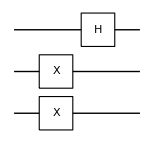

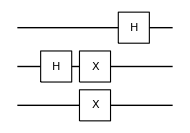

```mathematica
qc=QuantumCircuit[{S[2,1],S[3,1]},S[1,6]]
QuantumCircuit[S[2,6],qc]
```

```mathematica
Clear[v]
nn=Range[1,3];
vec=Ket[S[2]->1];
QuantumCircuit[vec,S[nn,6]]
```

-Graphics-

0_S_10_S_20_S_3

0_S_1+1_S_1

0_S_2+1_S_2

0_S_3+1_S_3

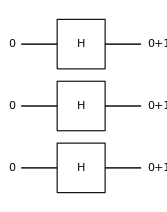

```mathematica
nn=Range[3];
v[1]=LogicalForm[Ket[],S[nn]]
v[2,1]=LogicalForm[Ket[]+Ket[S[1]->1]]
v[2,2]=LogicalForm[Ket[]+Ket[S[2]->1]]
v[2,3]=LogicalForm[Ket[]+Ket[S[3]->1]]
qc=QuantumCircuit[v[1],S[nn,6],v[2,1],v[2,2],v[2,3],
"PortSize"->{0.65,2}]
```

```mathematica
expr=Elaborate[qc];
expr//LogicalForm
```

(0_S_10_S_20_S_3)/(2 √2)+(0_S_10_S_21_S_3)/(2 √2)+(0_S_11_S_20_S_3)/(2 √2)+(0_S_11_S_21_S_3)/(2 √2)+(1_S_10_S_20_S_3)/(2 √2)+(1_S_10_S_21_S_3)/(2 √2)+(1_S_11_S_20_S_3)/(2 √2)+(1_S_11_S_21_S_3)/(2 √2)

You can give custom labels.

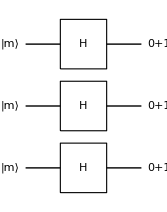

(0_S_10_S_20_S_3)/(2 √2)+(0_S_10_S_21_S_3)/(2 √2)+(0_S_11_S_20_S_3)/(2 √2)+(0_S_11_S_21_S_3)/(2 √2)+(1_S_10_S_20_S_3)/(2 √2)+(1_S_10_S_21_S_3)/(2 √2)+(1_S_11_S_20_S_3)/(2 √2)+(1_S_11_S_21_S_3)/(2 √2)

```mathematica
qc=QuantumCircuit[{v[1],"Label"->"|m⟩"},S[nn,6],v[2,1],v[2,2],v[2,3],
"PortSize"->{0.65,2}]
expr=Elaborate@qc;LogicalForm@expr
```

If the custom label is a list, then its elements are rotated.

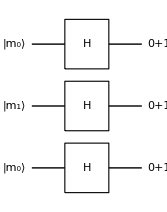

(0_S_10_S_20_S_3)/(2 √2)+(0_S_10_S_21_S_3)/(2 √2)+(0_S_11_S_20_S_3)/(2 √2)+(0_S_11_S_21_S_3)/(2 √2)+(1_S_10_S_20_S_3)/(2 √2)+(1_S_10_S_21_S_3)/(2 √2)+(1_S_11_S_20_S_3)/(2 √2)+(1_S_11_S_21_S_3)/(2 √2)

```mathematica
qc=QuantumCircuit[
{v[1],"Label"->{"|m_0⟩","|m_1⟩"}},
S[nn,6],v[2,1],v[2,2],v[2,3],
"PortSize"->{0.65,2}]
expr=Elaborate@qc;
LogicalForm@expr
```

```mathematica
nn=Range[3];
v[1]=LogicalForm[Ket[],S[nn]]
v[2]=ProductState[S[nn]->{1,1}]
QuantumCircuit[v[1],S[nn,6],v[2],
"PortSize"->{0.65,2}]
```

0_S_10_S_20_S_3

(0+1)_S_1⊗(0+1)_S_2⊗(0+1)_S_3

-Graphics-

Controlled-unitary gates

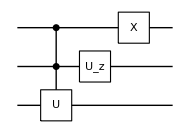

(1/8-ⅈ/16) (-3 ⅈ+√3) S_1^x S_2^z+1/16 (1-ⅈ √3) S_1^x S_3^y+1/16 ((-2-3 ⅈ)+(1+2 ⅈ) √3) S_1^y S_2^z+1/16 (ⅈ+√3) S_1^y S_3^y+1/16 ⅈ (ⅈ+√3) S_1^x S_2^z S_3^y+1/16 (-ⅈ-√3) S_1^y S_2^z S_3^y+1/16 ((3-2 ⅈ)+(6+ⅈ) √3) S_1^x+1/16 ((2+3 ⅈ)-(1+2 ⅈ) √3) S_1^y

(0 | 0 | 0 | 0 | 1/2 (-ⅈ+√3) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 (-ⅈ+√3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/4 (3+ⅈ √3) | 1/4 (-ⅈ-√3)
0 | 0 | 0 | 0 | 0 | 0 | 1/4 (ⅈ+√3) | 1/4 (3+ⅈ √3)
1/2 (-ⅈ+√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 (-ⅈ+√3) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 (ⅈ+√3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 (ⅈ+√3) | 0 | 0 | 0 | 0)

```mathematica
qc=QuantumCircuit[
ControlledU[S[{1,2}],Rotation[Pi/3,S[3,2],"Label"->"U"],"Label"->"R"],
Rotation[Pi/3,S[2,3]],
S[1,1]]
expr=ExpressionFor[qc]
mat=Simplify@Matrix[qc];
MatrixForm[mat]
```

## Grouping Circuit Elements With { }

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

In QuantumCircuitpaclet:Q3/ref/QuantumCircuitQ3 Package Symbol, Listpaclet:ref/List ({…}) can carry  two special meanings. First, it can put different quantum gates at the same time slice. Second, it can give options to particular quantum circuit elements.

### Putting different quantum logic gates at the same time slice.

Here all quantum logic gates are displayed at different time slices (along the horizontal direction).

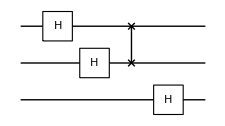

```mathematica
QuantumCircuit[S[1,6],S[2,6],SWAP[S[1],S[2]],S[3,6]]
```

Here the first two gates are displayed at the same time slice while others are separated long the time (horizontal) direction.

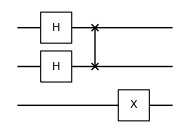

```mathematica
QuantumCircuit[{S[1,6],S[2,6]},SWAP[S[1],S[2]],S[3,1]]
```

WRONG USAGE: Here the Hadamardpaclet:Q3/ref/HadamardQ3 Package Symbol gate and the SWAPpaclet:Q3/ref/SWAPQ3 Package Symbol gate are displayed at the same time slice. First of all, it results in a bad graphical representation. But, more importantly, it is physically wrong because the Hadamard gate and SWAPpaclet:Q3/ref/SWAPQ3 Package Symbol do not commute with each other. Only mutually commuting quantum logic gates are allowed to be grouped together in QuantumCircuitpaclet:Q3/ref/QuantumCircuitQ3 Package Symbol.

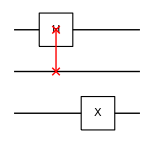

```mathematica
QuantumCircuit[{S[1,6],Red,SWAP[S[1],S[2]]},S[3,1]]
```

WRONG USAGE: It is not allowed to group vectors with operators as they are completely different in character. For example, while the circuit model qc1 is okay, Q3 complains about qc2.

```mathematica
vec=LogicalForm[Ket[],S@{1,2}]
qc1=QuantumCircuit[vec,S[1,3],S[2,3]]
qc2=QuantumCircuit[{vec,S[1,3]},S[2,3]]
```

0_S_10_S_2

-Graphics-

-Graphics-

Here you can see grouping two vectors is allowed and generates an expected result.

```mathematica
v=Ket[S[1]->1];
w=Ket[S[2]->1];
QuantumCircuit[{v,w},S[1,3]]
```

-Graphics-

```mathematica
QuantumCircuit[{v,w,"Label"->Ket[α]},S[1,3]]
```

-Graphics-

KNOWN ISSUE: This grouping feature does not work as expected when there is only a single grouping. For example, here two gates are supposed to be displayed at the same time slice, but apparently not. The bug will be fixed in a later release of Q3.

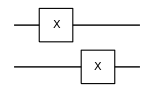

```mathematica
QuantumCircuit[{S[1,1],S[2,1]}]
```

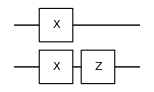

```mathematica
QuantumCircuit[{S[1,1],S[2,1]},S[2,3]]
```

### Giving options to particular quantum logic gates or input/output states

This is one of the simplest cases.

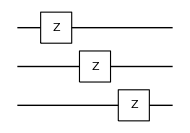

```mathematica
QuantumCircuit[S[1,3],S[2,3],S[3,3]]
```

In this example, the second and only the second gate is shown in red color.

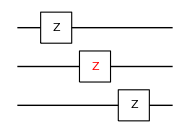

```mathematica
QuantumCircuit[S[1,3],{Red,S[2,3]},S[3,3]]
```

Unlike the example above, here all gates are displayed in red.

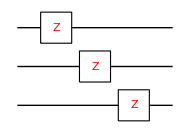

```mathematica
QuantumCircuit[Red,S[1,3],S[2,3],S[3,3]]
```

Here the second gate takes an option and it is labeled with “U” (not the default label “Z”).

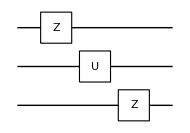

```mathematica
QuantumCircuit[S[1,3],{S[2,3],"Label"->"U"},S[3,3]]
```

## Automatic Conversion to Operator Expressions

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

Consider an example of the entangler circuit model.

-Graphics-

-Graphics-

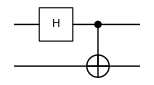

```mathematica
qc1=QuantumCircuit[S[1,6]]
qc2=QuantumCircuit[CNOT[S[1],S[2]]]
qc=QuantumCircuit[qc1,qc2]
```

This is the usual way to convert quantum circuit models into operator expressions.

```mathematica
op1=Elaborate[qc1]
op2=Elaborate[qc2]
op=Elaborate[qc]
```

S_1^x/(√2)+S_1^z/(√2)

1/2-1/2 S_1^z S_2^x+S_1^z/2+S_2^x/2

1/(2 √2)+(S_1^x S_2^x)/(2 √2)-(ⅈ S_1^y S_2^x)/(2 √2)+(S_1^z S_2^x)/(2 √2)+S_1^x/(2 √2)+(ⅈ S_1^y)/(2 √2)+S_1^z/(2 √2)-S_2^x/(2 √2)

```mathematica
op-op2**op1
```

0

The above can also be achieve directly regarding the quantum circuit models as operators.

```mathematica
new=qc2**qc1 (* Notice the order. *)
```

1/(2 √2)+(S_1^x S_2^x)/(2 √2)-(ⅈ S_1^y S_2^x)/(2 √2)+(S_1^z S_2^x)/(2 √2)+S_1^x/(2 √2)+(ⅈ S_1^y)/(2 √2)+S_1^z/(2 √2)-S_2^x/(2 √2)

```mathematica
op-new
```

0

## More Complicated Gates

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

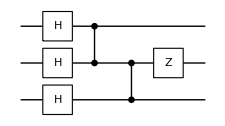

1/(4 √2)+(S_1^x S_3^x)/(4 √2)+(S_1^x S_3^z)/(4 √2)-(ⅈ S_1^y S_2^x)/(4 √2)-(S_1^y S_2^y)/(4 √2)-(ⅈ S_1^y S_2^z)/(4 √2)-(S_1^y S_3^y)/(4 √2)+(S_1^z S_3^x)/(4 √2)+(S_1^z S_3^z)/(4 √2)-(ⅈ S_2^x S_3^y)/(4 √2)-(S_2^y S_3^y)/(4 √2)-(ⅈ S_2^z S_3^y)/(4 √2)+(S_1^x S_2^x S_3^x)/(4 √2)+(S_1^x S_2^x S_3^z)/(4 √2)+(ⅈ S_1^x S_2^y S_3^x)/(4 √2)+(ⅈ S_1^x S_2^y S_3^z)/(4 √2)+(S_1^x S_2^z S_3^x)/(4 √2)+(S_1^x S_2^z S_3^z)/(4 √2)+(S_1^y S_2^x S_3^y)/(4 √2)-(ⅈ S_1^y S_2^y S_3^y)/(4 √2)+(S_1^y S_2^z S_3^y)/(4 √2)+(S_1^z S_2^x S_3^x)/(4 √2)+(S_1^z S_2^x S_3^z)/(4 √2)+(ⅈ S_1^z S_2^y S_3^x)/(4 √2)+(ⅈ S_1^z S_2^y S_3^z)/(4 √2)+(S_1^z S_2^z S_3^x)/(4 √2)+(S_1^z S_2^z S_3^z)/(4 √2)+(ⅈ S_1^y)/(4 √2)-S_2^x/(4 √2)+(ⅈ S_2^y)/(4 √2)-S_2^z/(4 √2)+(ⅈ S_3^y)/(4 √2)

{0.004722,Null}

{0.004528,Null}

(1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2)
1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2)
-1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2)
1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2)
1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2)
1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2)
1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2)
-1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2))

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
qc=QuantumCircuit[
S[{1,2,3},6],
CZ[S[1],S[2]],
CZ[S[2],S[3]],
S[2,3]
]
expr=ExpressionFor[qc]
Timing[mat1=Matrix[qc];]
Timing[mat2=Matrix[qc];]
mat2//MatrixForm
mat1-mat2//MatrixForm
```

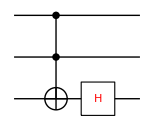

```mathematica
qc=QuantumCircuit[
Toffoli[S[1],S[2],S[3]],
Red,S[3,6]
]
```

```mathematica
op=Elaborate[qc]
expr=S[3,6]**Toffoli[S[1],S[2],S[3]]//Elaborate
op-expr//Garner
```

1/(4 √2)+(S_1^z S_2^z)/(4 √2)+(S_1^z S_3^x)/(4 √2)-(ⅈ S_1^z S_3^y)/(4 √2)+(S_1^z S_3^z)/(4 √2)+(S_2^z S_3^x)/(4 √2)-(ⅈ S_2^z S_3^y)/(4 √2)+(S_2^z S_3^z)/(4 √2)-(S_1^z S_2^z S_3^x)/(4 √2)+(ⅈ S_1^z S_2^z S_3^y)/(4 √2)-(S_1^z S_2^z S_3^z)/(4 √2)-S_1^z/(4 √2)-S_2^z/(4 √2)+(3 S_3^x)/(4 √2)+(ⅈ S_3^y)/(4 √2)+(3 S_3^z)/(4 √2)

1/(4 √2)+(S_1^z S_2^z)/(4 √2)+(S_1^z S_3^x)/(4 √2)-(ⅈ S_1^z S_3^y)/(4 √2)+(S_1^z S_3^z)/(4 √2)+(S_2^z S_3^x)/(4 √2)-(ⅈ S_2^z S_3^y)/(4 √2)+(S_2^z S_3^z)/(4 √2)-(S_1^z S_2^z S_3^x)/(4 √2)+(ⅈ S_1^z S_2^z S_3^y)/(4 √2)-(S_1^z S_2^z S_3^z)/(4 √2)-S_1^z/(4 √2)-S_2^z/(4 √2)+(3 S_3^x)/(4 √2)+(ⅈ S_3^y)/(4 √2)+(3 S_3^z)/(4 √2)

0

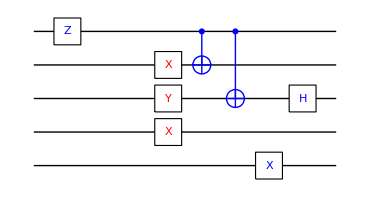

```mathematica
qc=QuantumCircuit[Blue,S[1,3],
"Spacer","Spacer",
{Red,S[2,1],S[3,2],S[4,1]},
{Blue, CNOT[S[1],S[2]] },
 CNOT[S[1],S[3]],
S[5,1],
S[3,6],
Opts->"A"
]
```

```mathematica
op=Elaborate[qc]
expr=Multiply@@Reverse@{
S[1,3],S[2,1],S[3,2],S[4,1],CNOT[S[1],S[2]],CNOT[S[1],S[3]],S[5,1],S[3,6]}//Elaborate
op-expr//Garner
```

-(ⅈ S_4^x S_5^x)/(2 √2)+(ⅈ S_1^z S_4^x S_5^x)/(2 √2)-(S_3^y S_4^x S_5^x)/(2 √2)+(S_1^z S_3^y S_4^x S_5^x)/(2 √2)-(ⅈ S_2^x S_3^x S_4^x S_5^x)/(2 √2)+(ⅈ S_2^x S_3^z S_4^x S_5^x)/(2 √2)-(ⅈ S_1^z S_2^x S_3^x S_4^x S_5^x)/(2 √2)+(ⅈ S_1^z S_2^x S_3^z S_4^x S_5^x)/(2 √2)

-(ⅈ S_4^x S_5^x)/(2 √2)+(ⅈ S_1^z S_4^x S_5^x)/(2 √2)-(S_3^y S_4^x S_5^x)/(2 √2)+(S_1^z S_3^y S_4^x S_5^x)/(2 √2)-(ⅈ S_2^x S_3^x S_4^x S_5^x)/(2 √2)+(ⅈ S_2^x S_3^z S_4^x S_5^x)/(2 √2)-(ⅈ S_1^z S_2^x S_3^x S_4^x S_5^x)/(2 √2)+(ⅈ S_1^z S_2^x S_3^z S_4^x S_5^x)/(2 √2)

0

## With Inputs and Outputs

You can specifies input and output states.

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Real,a,b,c]
```

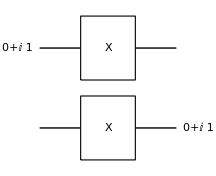

```mathematica
v1=Ket[]+I Ket[S[1]->1];
v2=Ket[]+I Ket[S[2]->1];
qc=QuantumCircuit[
v1,S[{1,2},1],v2,
"PortSize"->2]
```

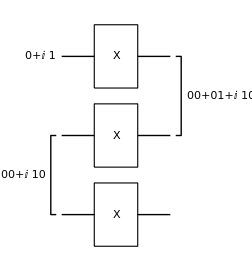

```mathematica
v3=LogicalForm[Ket[]+I Ket[S[1]->1]+Ket[S[2]->1],S[{1,2}]];
v4=LogicalForm[Ket[]+I Ket[S[2]->1],S[{2,3}]];
qc=QuantumCircuit[
v1,v4,S[{1,2,3},1],v3,
"UnitLength"->42,
"PortSize"->2
]
```

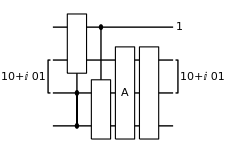

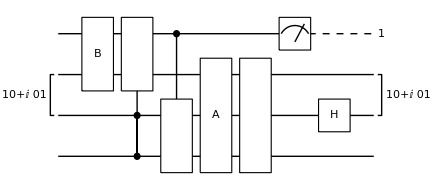

```mathematica
Clear[expr,vec,mat];
expr[1]=S[2,1]+I S[4,3];
v1=Ket[S[2]->1]+ I Ket[S[3]->1];
mat[0]=ThePauli[1,3];
expr[2]=ExpressionFor[mat[0],S[{1,2}]];
qc=QuantumCircuit[v1,
ControlledU[S[{3,4}],S[1,1]-S[2,2]],
ControlledU[S[1],S[3,2]+I S[4,1]],
{expr[1],"Label"->"A"},
expr[1],{Ket[S[1]->1],v1}
]
qc=QuantumCircuit[{expr[2],"Label"->"B"},
qc,Measurement[S[1]],S[3,6],
"PortSize"->2]
```

```mathematica
expr[0]=ExpressionFor[qc]
vec[0]=Matrix[qc];
vec[0]//MatrixForm
```

(1_S_1)/(2 √2)-(ⅈ 1_S_11_S_21_S_31_S_4)/(2 √2)+(ⅈ 1_S_11_S_2)/(2 √2)+(ⅈ 1_S_11_S_21_S_3)/(2 √2)+(ⅈ 1_S_11_S_21_S_4)/(2 √2)-(1_S_11_S_3)/(2 √2)-(1_S_11_S_31_S_4)/(2 √2)-(1_S_11_S_4)/(2 √2)

(0
0
0
0
0
0
0
0
1/(2 √2)
-1/(2 √2)
-1/(2 √2)
-1/(2 √2)
ⅈ/(2 √2)
ⅈ/(2 √2)
ⅈ/(2 √2)
-ⅈ/(2 √2))

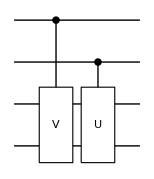

1/4+1/4 S_1^z S_2^z+1/2 ⅈ S_3^y S_4^x-1/2 S_1^z S_2^z S_3^y-1/2 ⅈ S_1^z S_2^z S_4^x-1/2 ⅈ S_1^z S_3^y S_4^x-1/2 ⅈ S_2^z S_3^y S_4^x+1/2 ⅈ S_1^z S_2^z S_3^y S_4^x+S_1^z/4+S_2^z/4+S_3^y/2+(ⅈ S_4^x)/2

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0)

```mathematica
expr[1]=S[2,1]+I S[4,3];
qc=QuantumCircuit[
ControlledU[S[1],S[3,2]+I S[4,1],"Label"->"V"],
ControlledU[S[2],S[3,2]+I S[4,1],"Label"->"U"]
]
expr[0]=ExpressionFor[qc]
mat[0]=Matrix[qc];
mat[0]//MatrixForm
```

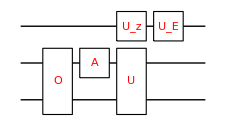

1/2 ⅈ (ⅈ+√3) Cos[b/2] Cos[1/2 (a+c+ϕ)] S_2^z+1/2 (ⅈ+√3) Cos[1/2 (a-c-ϕ)] S_1^y S_2^z Sin[b/2]-1/2 (ⅈ+√3) S_1^x S_2^z Sin[b/2] Sin[1/2 (a-c-ϕ)]-1/2 S_1^x S_2^x S_4^z Sin[b/2] (2 (1+(-1)^(1/3)) Cos[ϕ/2] Sin[(a-c)/2]+(-3-ⅈ √3) Cos[(a-c)/2] Sin[ϕ/2])+1/2 Cos[b/2] S_1^z S_2^x S_4^z (2 (1+(-1)^(1/3)) Cos[ϕ/2] Sin[(a+c)/2]+(3+ⅈ √3) Cos[(a+c)/2] Sin[ϕ/2])+1/2 S_1^y S_2^x S_4^z Sin[b/2] (2 (1+(-1)^(1/3)) Cos[(a-c)/2] Cos[ϕ/2]+(3+ⅈ √3) Sin[(a-c)/2] Sin[ϕ/2])+1/2 Cos[b/2] S_2^x S_4^z (2 (ⅈ+(-1)^(5/6)) Cos[(a+c)/2] Cos[ϕ/2]+(-3 ⅈ+√3) Sin[(a+c)/2] Sin[ϕ/2])+1/2 (ⅈ+√3) Cos[b/2] S_1^z S_2^z Sin[1/2 (a+c+ϕ)]

(1/2 (ⅈ+√3) Cos[b/2] (ⅈ Cos[1/2 (a+c+ϕ)]+Sin[1/2 (a+c+ϕ)]) | 0 | -1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]-ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (1-ⅈ √3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]-ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]-ⅈ Sin[1/2 (a-c-ϕ)]) | 0
0 | 1/2 (ⅈ+√3) Cos[b/2] (ⅈ Cos[1/2 (a+c+ϕ)]+Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]-ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (1-ⅈ √3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]-ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | -1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]-ⅈ Sin[1/2 (a-c-ϕ)])
-1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]-ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (1-ⅈ √3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]-ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]-ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (ⅈ+√3) Sin[b/2] (ⅈ Cos[1/2 (a-c-ϕ)]+Sin[1/2 (a-c-ϕ)]) | 0
0 | 1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]-ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (1-ⅈ √3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]-ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | -1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]-ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (ⅈ+√3) Sin[b/2] (ⅈ Cos[1/2 (a-c-ϕ)]+Sin[1/2 (a-c-ϕ)])
1/2 ⅈ (ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | -1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 ⅈ (ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | -1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]) | 0
0 | 1/2 ⅈ (ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 ⅈ (ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)])
-1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (1-ⅈ √3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | -1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (1-ⅈ √3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]) | 0
0 | 1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (1-ⅈ √3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (1-ⅈ √3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]))

```mathematica
Let[Real,ϕ]
qc=QuantumCircuit[
Red,{expr[1],"Label"->"O"},
Phase[Pi/3,S[2],"Label"->"A"],
{Rotation[ϕ,S[1,3]],
{expr[1],"Label"->"U"}},
EulerRotation[{a,b,c},S[1]]
]
expr[0]=ExpressionFor[qc]
mat[0]=Simplify@Matrix[qc];
mat[0]//MatrixForm
```

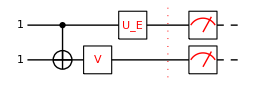

```mathematica
Let[Real,ϕ,a,b,c]
expr[1]=S[2,1]+I S[3,3];
qc=QuantumCircuit[
Ket[S[{1,2}]->1],
CNOT[S[1],S[2]],Red,
Rotation[ϕ,S[2,3],"Label"->"V"],
EulerRotation[{a,b,c},S[1]],
"Separator",
Measurement[S[{1,2}]]
]
```

```mathematica
expr[0]=ExpressionFor[qc]
vec[0]=Simplify@Matrix[qc];
vec[0]//MatrixForm
```

Measurement::nonum: Cannot perform a measurement on a nonnumeric state vector. Probability half is assumed.

-(␣ Sin[b/2] (Cos[1/2 (a-c+ϕ)]-ⅈ Sin[1/2 (a-c+ϕ)]))/(√(Sin[b/2]^2))

Measurement::nonum: Cannot perform a measurement on a nonnumeric state vector. Probability half is assumed.

(0
0
(Cos[b/2] (Cos[1/2 (a+c-ϕ)]+ⅈ Sin[1/2 (a+c-ϕ)]))/(√(Cos[b/2]^2))
0)

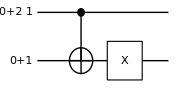

␣+2 1_S_1+2 1_S_11_S_2+1_S_2

(1
1
2
2)

```mathematica
qc=QuantumCircuit[
ProductState[S[1]->{1,2},S[2]->{1,1}],
CNOT[S[1],S[2]],
S[2,1],
"PortSize"->{1.5,0.65}
]
expr[0]=ExpressionFor[qc]
vec[0]=Matrix[qc];
vec[0]//MatrixForm
```

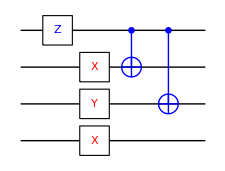

```mathematica
qc=QuantumCircuit[Blue,S[1,3],
{Red,S[2,1],S[3,2],S[4,1]},
{Blue, CNOT[S[1],S[2]] },
 CNOT[S[1],S[3]]
]
```

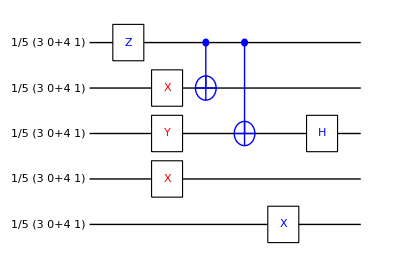

-(96 ⅈ √2 ␣)/3125+(96 ⅈ √2 1_S_1)/3125+(128 ⅈ √2 1_S_11_S_2)/3125-(672 ⅈ √2 1_S_11_S_21_S_31_S_4)/3125-(504 ⅈ √2 1_S_11_S_21_S_31_S_41_S_5)/3125-(672 ⅈ √2 1_S_11_S_21_S_31_S_5)/3125-(896 ⅈ √2 1_S_11_S_21_S_3)/3125+(72 ⅈ √2 1_S_11_S_21_S_41_S_5)/3125+(96 ⅈ √2 1_S_11_S_21_S_4)/3125+(96 ⅈ √2 1_S_11_S_21_S_5)/3125-(672 ⅈ √2 1_S_11_S_3)/3125-(378 ⅈ √2 1_S_11_S_31_S_41_S_5)/3125-(504 ⅈ √2 1_S_11_S_31_S_4)/3125-(504 ⅈ √2 1_S_11_S_31_S_5)/3125+(72 ⅈ √2 1_S_11_S_4)/3125+(54 ⅈ √2 1_S_11_S_41_S_5)/3125+(72 ⅈ √2 1_S_11_S_5)/3125-(504 ⅈ √2 1_S_21_S_3)/3125-(567 ⅈ 1_S_21_S_31_S_41_S_5)/(3125 √2)-(54 ⅈ √2 1_S_21_S_4)/3125-(81 ⅈ 1_S_21_S_41_S_5)/(3125 √2)-(54 ⅈ √2 1_S_21_S_5)/3125-(72 ⅈ √2 1_S_2)/3125-(378 ⅈ √2 1_S_21_S_31_S_4)/3125-(378 ⅈ √2 1_S_21_S_31_S_5)/3125-(504 ⅈ √2 1_S_31_S_4)/3125-(378 ⅈ √2 1_S_31_S_41_S_5)/3125-(504 ⅈ √2 1_S_31_S_5)/3125-(672 ⅈ √2 1_S_3)/3125-(54 ⅈ √2 1_S_41_S_5)/3125-(72 ⅈ √2 1_S_4)/3125-(72 ⅈ √2 1_S_5)/3125

{-(96 ⅈ √2)/3125,-(72 ⅈ √2)/3125,-(72 ⅈ √2)/3125,-(54 ⅈ √2)/3125,-(672 ⅈ √2)/3125,-(504 ⅈ √2)/3125,-(504 ⅈ √2)/3125,-(378 ⅈ √2)/3125,-(72 ⅈ √2)/3125,-(54 ⅈ √2)/3125,-(54 ⅈ √2)/3125,-(81 ⅈ)/(3125 √2),-(504 ⅈ √2)/3125,-(378 ⅈ √2)/3125,-(378 ⅈ √2)/3125,-(567 ⅈ)/(3125 √2),(96 ⅈ √2)/3125,(72 ⅈ √2)/3125,(72 ⅈ √2)/3125,(54 ⅈ √2)/3125,-(672 ⅈ √2)/3125,-(504 ⅈ √2)/3125,-(504 ⅈ √2)/3125,-(378 ⅈ √2)/3125,(128 ⅈ √2)/3125,(96 ⅈ √2)/3125,(96 ⅈ √2)/3125,(72 ⅈ √2)/3125,-(896 ⅈ √2)/3125,-(672 ⅈ √2)/3125,-(672 ⅈ √2)/3125,-(504 ⅈ √2)/3125}

```mathematica
qc=QuantumCircuit[
ProductState[S[{1,2,3,4,5}]->{3,4}/5],
Blue,S[1,3],
{Red,S[2,1],S[3,2],S[4,1]},
{Blue, CNOT[S[1],S[2]] },
 CNOT[S[1],S[3]],
S[5,1],S[3,6],
"PortSize"->2
]
expr[0]=ExpressionFor[qc]
vec[0]=Simplify@Matrix[qc];
vec[0]//Normal
```

## Example with GraphStates

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

Let us consider the graph states.



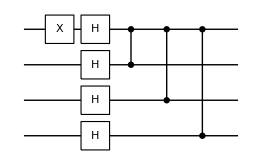

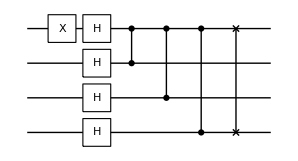

1/8 S_1^x S_4^x-1/8 ⅈ S_1^x S_4^y-1/8 S_1^y S_2^y-1/8 S_1^y S_3^y-1/8 ⅈ S_1^y S_4^z-1/8 ⅈ S_1^z S_2^y-1/8 ⅈ S_1^z S_3^y+1/8 S_1^z S_4^z+1/8 S_2^x S_3^x+1/8 S_2^x S_3^z-1/8 ⅈ S_2^y S_4^x-1/8 S_2^y S_4^y+1/8 S_2^z S_3^x+1/8 S_2^z S_3^z-1/8 ⅈ S_3^y S_4^x-1/8 S_3^y S_4^y+1/8 S_1^x S_2^x S_3^x+1/8 S_1^x S_2^x S_3^z+1/8 ⅈ S_1^x S_2^y S_4^x+1/8 S_1^x S_2^y S_4^y+1/8 S_1^x S_2^z S_3^x+1/8 S_1^x S_2^z S_3^z+1/8 ⅈ S_1^x S_3^y S_4^x+1/8 S_1^x S_3^y S_4^y-1/8 ⅈ S_1^y S_2^y S_3^y+1/8 S_1^y S_2^y S_4^z+1/8 S_1^y S_3^y S_4^z+1/8 S_1^z S_2^y S_3^y+1/8 ⅈ S_1^z S_2^y S_4^z+1/8 ⅈ S_1^z S_3^y S_4^z+1/8 S_2^x S_3^x S_4^z+1/8 S_2^x S_3^z S_4^z+1/8 S_2^y S_3^y S_4^x-1/8 ⅈ S_2^y S_3^y S_4^y+1/8 S_2^z S_3^x S_4^z+1/8 S_2^z S_3^z S_4^z+1/8 S_1^x S_2^x S_3^x S_4^z+1/8 S_1^x S_2^x S_3^z S_4^z-1/8 S_1^x S_2^y S_3^y S_4^x+1/8 ⅈ S_1^x S_2^y S_3^y S_4^y+1/8 S_1^x S_2^z S_3^x S_4^z+1/8 S_1^x S_2^z S_3^z S_4^z+1/8 ⅈ S_1^y S_2^x S_3^x S_4^x-1/8 S_1^y S_2^x S_3^x S_4^y+1/8 ⅈ S_1^y S_2^x S_3^z S_4^x-1/8 S_1^y S_2^x S_3^z S_4^y+1/8 ⅈ S_1^y S_2^y S_3^y S_4^z+1/8 ⅈ S_1^y S_2^z S_3^x S_4^x-1/8 S_1^y S_2^z S_3^x S_4^y+1/8 ⅈ S_1^y S_2^z S_3^z S_4^x-1/8 S_1^y S_2^z S_3^z S_4^y+1/8 S_1^z S_2^x S_3^x S_4^x+1/8 ⅈ S_1^z S_2^x S_3^x S_4^y+1/8 S_1^z S_2^x S_3^z S_4^x+1/8 ⅈ S_1^z S_2^x S_3^z S_4^y-1/8 S_1^z S_2^y S_3^y S_4^z+1/8 S_1^z S_2^z S_3^x S_4^x+1/8 ⅈ S_1^z S_2^z S_3^x S_4^y+1/8 S_1^z S_2^z S_3^z S_4^x+1/8 ⅈ S_1^z S_2^z S_3^z S_4^y+(ⅈ S_1^y)/8-S_1^z/8-S_4^x/8+(ⅈ S_4^y)/8

```mathematica
g=Graph[{S[1]<->S[2],S[1]<->S[3],S[1]<->S[4]}]
qc=QuantumCircuit[S[1,1],g]
qc=QuantumCircuit[qc,SWAP[S[1],S[4]]]
Elaborate[qc]
```

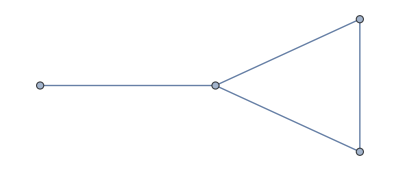

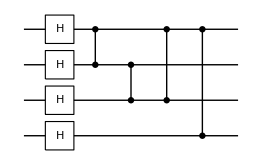

```mathematica
g=Graph[{S[1]<->S[2],S[2]<->S[3],S[1]<->S[3],S[1]<->S[4]}]
QuantumCircuit[g]
```

0_S_10_S_20_S_30_S_4

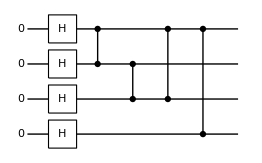

␣/4-1/4 1_S_11_S_2-1/4 1_S_11_S_21_S_3+(1_S_1)/4+1/4 1_S_11_S_21_S_31_S_4+1/4 1_S_11_S_21_S_4-1/4 1_S_11_S_3+1/4 1_S_11_S_31_S_4-1/4 1_S_11_S_4-1/4 1_S_21_S_3-1/4 1_S_21_S_31_S_4+(1_S_2)/4+1/4 1_S_21_S_4+(1_S_3)/4+1/4 1_S_31_S_4+(1_S_4)/4

{1/4,1/4,1/4,1/4,1/4,1/4,-1/4,-1/4,1/4,-1/4,-1/4,1/4,-1/4,1/4,-1/4,1/4}

␣/4-1/4 1_S_11_S_2-1/4 1_S_11_S_21_S_3+(1_S_1)/4+1/4 1_S_11_S_21_S_31_S_4+1/4 1_S_11_S_21_S_4-1/4 1_S_11_S_3+1/4 1_S_11_S_31_S_4-1/4 1_S_11_S_4-1/4 1_S_21_S_3-1/4 1_S_21_S_31_S_4+(1_S_2)/4+1/4 1_S_21_S_4+(1_S_3)/4+1/4 1_S_31_S_4+(1_S_4)/4

0

```mathematica
in=LogicalForm[Ket[],S[{1,2,3,4}]]
qc=QuantumCircuit[in,g]
v[1]=Elaborate[qc]
v[2]=Matrix[qc];
v[2]//Normal
v[3]=GraphState[g]
v[1]-v[3]//Simplify//Normal
```

## Examples with Measurements

Here are simple examples with measurements.

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

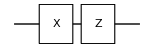

-1_S_1

```mathematica
qc=QuantumCircuit[Ket[],S[1,1],S[1,3]]
ex=ExpressionFor[qc]
```

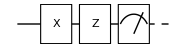

-1_S_1

```mathematica
qc=QuantumCircuit[Ket[],S[1,1],S[1,3],Measurement[S[1]]]
ex=ExpressionFor[qc]
```

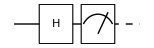

1_S_1

```mathematica
qc=QuantumCircuit[Ket[],S[1,6],Measurement[S[1]]]
ex=ExpressionFor[qc]
```

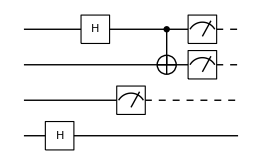

```mathematica
qc=QuantumCircuit[
Ket[],
S[4,6],S[1,6],
Measurement[S[3]],
CNOT[S[1],S[2]],
Measurement[S@{1,2}]
]
```

```mathematica
cc=(ExpressionFor@qc)//Simplify;
ccc=LogicalForm[cc,S[{1,2,3,4}]]
KetFactor[ccc,S[{1,2}]]
```

(1_S_11_S_20_S_30_S_4+1_S_11_S_20_S_31_S_4)/(√2)

(1_S_11_S_20_S_3⊗(0_S_4+1_S_4))/(√2)

Take another example

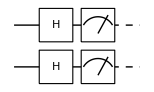

```mathematica
qc=QuantumCircuit[Ket[],{S[1,6],S[2,6]},Measurement[S[{1,2}]]]
```

```mathematica
data=Table[(result=ExpressionFor[qc];Readout[result,S[{1,2}]]),{200}];
Histogram3D[data,AxesLabel->{S[1,],S[2,],"Counts"}]
```

-Graphics3D-

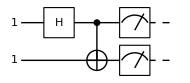

```mathematica
qc=QuantumCircuit[
Ket[S[{1,2}]->1],
S[1,6],CNOT[S[1],S[2]],
{Measurement[S[1]],Measurement[S[2]]}
]
```

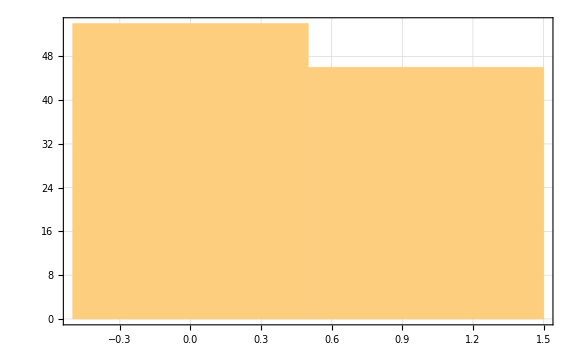

```mathematica
data=Table[(result=ExpressionFor[qc];Readout[result,S[1]]),{100}];
Histogram[data,Axes->False,Frame->True,FrameStyle->Large]
```

(0_S_11_S_2-1_S_10_S_2)/(√2)

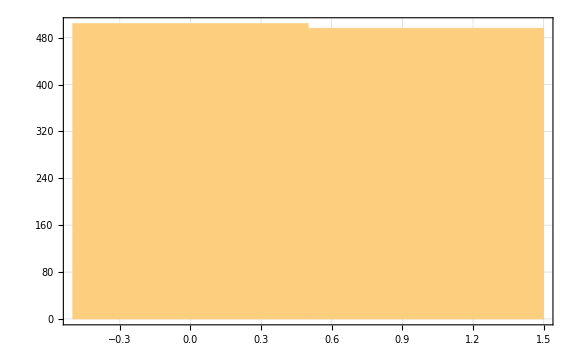

```mathematica
v=CNOT[S[1],S[2]]**S[1,6]**Ket[S[{1,2}]->1]//Simplify;
v//LogicalForm
data=Table[
u=Measurement[Measurement[v,S[2]],S[1]];
Readout[u,S[1]],
{j,1000}
];
Histogram[data]
```

## Examples with Controlled-U Gates

```mathematica
<<Q3`
```

Here are simple examples involving controlled-U gates.

```mathematica
Let[Qubit,S]
```

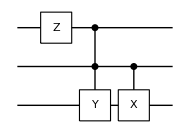

```mathematica
QuantumCircuit[
S[1,3],
ControlledU[S[{1,2}],S[3,2]],
ControlledU[S[2],S[3,1]]
]
```

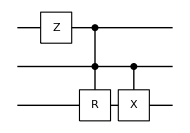

```mathematica
QuantumCircuit[
S[1,3],
ControlledU[S[{1,2}],Rotation[Pi/3,S[3,2]],"Label"->"R"],
ControlledU[S[2],S[3,1]]
]
```

## Examples with Arbitrary Controlled-U Gates

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

S_3^x-ⅈ S_3^y+S_4^z/2

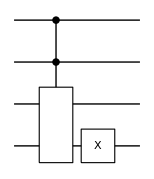

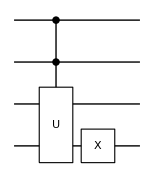

```mathematica
expr=S[3,1]- I S[3,2] + S[4,3]/2
qc1=QuantumCircuit[ControlledU[S[{1,2}],expr],S[4,1]]
qc2=QuantumCircuit[ControlledU[S[{1,2}],expr,"Label"->"U"],S[4,1]]
```

```mathematica
ex1=ExpressionFor[qc1]//Simplify
ex2=ExpressionFor[qc2]//Simplify
ex1-ex2//Simplify
```

1/8 (2 S_1^z S_4^x+ⅈ (S_1^z S_4^y-2 ⅈ S_2^z S_4^x+S_2^z S_4^y-2 ⅈ S_3^x S_4^x-2 S_3^y S_4^x+2 ⅈ S_1^z S_2^z S_4^x-S_1^z S_2^z S_4^y+2 ⅈ S_1^z S_3^x S_4^x+2 S_1^z S_3^y S_4^x+2 ⅈ S_2^z S_3^x S_4^x+2 S_2^z S_3^y S_4^x-2 ⅈ S_1^z S_2^z S_3^x S_4^x-2 S_1^z S_2^z S_3^y S_4^x-6 ⅈ S_4^x-S_4^y))

1/8 (2 S_1^z S_4^x+ⅈ (S_1^z S_4^y-2 ⅈ S_2^z S_4^x+S_2^z S_4^y-2 ⅈ S_3^x S_4^x-2 S_3^y S_4^x+2 ⅈ S_1^z S_2^z S_4^x-S_1^z S_2^z S_4^y+2 ⅈ S_1^z S_3^x S_4^x+2 S_1^z S_3^y S_4^x+2 ⅈ S_2^z S_3^x S_4^x+2 S_2^z S_3^y S_4^x-2 ⅈ S_1^z S_2^z S_3^x S_4^x-2 S_1^z S_2^z S_3^y S_4^x-6 ⅈ S_4^x-S_4^y))

0

Let us take another example, where the (multi-qubit) gate (operator) is expressed in an expression of Pauli operators for labelled qubits.

```mathematica
Let[Qubit,S]
```

S_3^0+ⅈ S_4^x

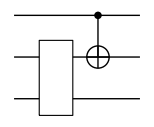

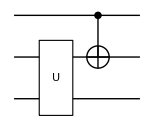

```mathematica
expr=S[3,0]+I S[4,1]
qc1=QuantumCircuit[ expr,CNOT[S[1],S[3]]]
qc2=QuantumCircuit[ {expr,"Label"->"U"},CNOT[S[1],S[3]]]
```

```mathematica
ExpressionFor[qc1]//Elaborate//Simplify
ExpressionFor[qc2]//Elaborate//Simplify
```

1/2 (1-S_1^z S_3^x+ⅈ S_1^z S_4^x+ⅈ S_3^x S_4^x-ⅈ S_1^z S_3^x S_4^x+S_1^z+S_3^x+ⅈ S_4^x)

1/2 (1-S_1^z S_3^x+ⅈ S_1^z S_4^x+ⅈ S_3^x S_4^x-ⅈ S_1^z S_3^x S_4^x+S_1^z+S_3^x+ⅈ S_4^x)

The gate is expressed in a matrix representation.

(ⅈ | 1
1 | -ⅈ)

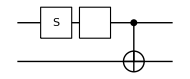

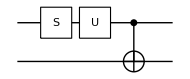

```mathematica
mat=ThePauli[1]+I ThePauli[3];
mat//MatrixForm
op=ExpressionFor[mat,S[1]];
qc1=QuantumCircuit[S[1,7], op,CNOT[S[1],S[3]]]
qc2=QuantumCircuit[ S[1,7],{op,"Label"->"U"},CNOT[S[1],S[3]]]
```

```mathematica
ex1=qc1//Elaborate//Simplify
ex2=qc2//Elaborate//Simplify
ex1-ex2//Simplify
```

1/2 (ⅈ+S_1^x S_3^x-ⅈ S_1^y S_3^x-S_1^z S_3^x+ⅈ S_1^x-S_1^y+ⅈ S_1^z+S_3^x)

1/2 (ⅈ+S_1^x S_3^x-ⅈ S_1^y S_3^x-S_1^z S_3^x+ⅈ S_1^x-S_1^y+ⅈ S_1^z+S_3^x)

0

Multi-qubit gate is expressed in a matrix representation.

(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)

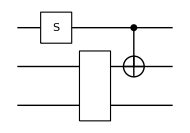

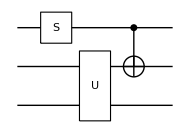

```mathematica
mat=ThePauli[1,2];
mat//MatrixForm
qq=S[{3,4}];
op=ExpressionFor[mat,qq];
qc1=QuantumCircuit[S[1,7], op,CNOT[S[1],S[3]]]
qc2=QuantumCircuit[ S[1,7],{op,"Label"->"U"},CNOT[S[1],S[3]]]
```

```mathematica
Elaborate[qc1]//Simplify
Elaborate[qc2]//Simplify
```

1/2 (-ⅈ S_1^z S_4^y+S_3^x S_4^y+S_1^z S_3^x S_4^y+ⅈ S_4^y)

1/2 (-ⅈ S_1^z S_4^y+S_3^x S_4^y+S_1^z S_3^x S_4^y+ⅈ S_4^y)

## Matrix on QuantumCircuit

Depending on the ratio of the “size” (the number of qubits) and the “depth” (the number of operations), Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol is more efficient than the ExpressionForpaclet:Q3/ref/ExpressionForQ3 Package Symbol.

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

```mathematica
$N=5;
ss=S[Range[$N],None]
```

{S_1,S_2,S_3,S_4,S_5}

```mathematica
CP[j_,j_]:=S[j,6]
CP[j_,k_]:=ControlledU[S[j],
Phase[Pi Power[2,k-j],S[k],"Label"->Subscript["R",j-k]]
]/;j>k
CP[j_,k_]:=ControlledU[S[j],
Phase[Pi Power[2,j-k],S[k],"Label"->Subscript["R",k-j]]
]/;j<k
SW[j_]:=SWAP[S[j],S[$N-j+1]]
```

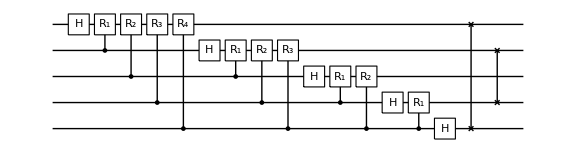

```mathematica
swaps=Table[SW[j],{j,1,$N/2}];
gates4a=Catenate@Table[CP[j,k],{k,1,$N},{j,k,$N}];
qft4a=Join[gates4a,swaps];
qc4a=QuantumCircuit[Sequence@@qft4a,ImageSize->Large]
```

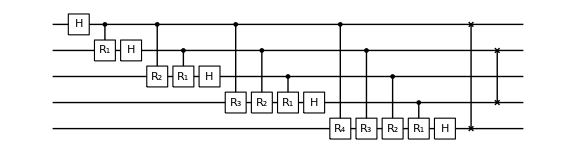

```mathematica
swaps=Table[SW[j],{j,1,$N/2}];
gates4b=Catenate@Table[CP[j,k],{k,1,$N},{j,1,k}];
qft4b=Join[gates4b,swaps];
qc4b=QuantumCircuit[Sequence@@qft4b,ImageSize->Large]
```

```mathematica
Timing[mat4a=Matrix[qc4a];]
Timing[mat4b=Matrix[qc4b];]
mat4a-mat4b//Simplify//Normal//Flatten//DeleteCases[#,0]&
Timing[mat4a=Matrix[qc4a];]
Timing[mat4b=Matrix[qc4b];]
mat4a-mat4b//Simplify//Normal//Flatten//DeleteCases[#,0]&
```

{0.402579,Null}

{0.356583,Null}

{}

{1.06257,Null}

{0.35838,Null}

{}

WARNING: The following takes quite long, sometime even fails, as the circuit is pretty deep compared with the size.

```mathematica
Timing[op4a=ExpressionFor[qc4a];]
```

{743.31,Null}

```mathematica
Timing[mat4c=Matrix[op4a];]
```

{0.000137,Null}

```mathematica
mat4a-mat4c//N//Chop//Normal
```

Thread::tdlen: Objects of unequal length in SparseArray[Automatic,«2»,{1,{{0,32,64,96,128,160,192,224,256,288,320,352,384,416,448,480,512,544,576,608,640,672,704,736,768,800,832,864,896,928,960,992,1024},{{1},{2},{3},{4},{5},{6},{7},«1010»,{26},{27},{28},{29},{30},{31},{32}}},{((Times[«2»]+Times[«2»]+Times[«2»])^3 (1/2 Plus[«3»]+1/4 Plus[«3»]+1/4 Plus[«3»]) (Times[«2»]+Times[«2»]+Times[«2»])^2)/(4 √2),«9»,«1014»}}]+«1» cannot be combined.

Thread::tdlen: Objects of unequal length in SparseArray[Automatic,{2,2},0.,{1,{{0,1,2},{{1},{2}}},{-1. op4a,-1. op4a}}]+SparseArray[Automatic,«2»,{1,{{0,32,«29»,992,1024},«1»},{0.176777+0. ⅈ,0.176777+0. ⅈ,0.176777+0. ⅈ,«1018»,0.146984+0.0982119 ⅈ,0.16332+0.0676495 ⅈ,0.17338+0.0344874 ⅈ}}] cannot be combined.

Thread::tdlen: Objects of unequal length in SparseArray[Automatic,{2,2},0,{1,{{0,1,2},{{1},{2}}},{-1. op4a,-1. op4a}}]+SparseArray[«1»] cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

{{-1. op4a,0},{0,-1. op4a}}+{{0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777,0.176777},{0.176777,0.17338+0.0344874 ⅈ,0.16332+0.0676495 ⅈ,0.146984+0.0982119 ⅈ,0.125+0.125 ⅈ,0.0982119+0.146984 ⅈ,0.0676495+0.16332 ⅈ,0.0344874+0.17338 ⅈ,0.+0.176777 ⅈ,-0.0344874+0.17338 ⅈ,-0.0676495+0.16332 ⅈ,-0.0982119+0.146984 ⅈ,-0.125+0.125 ⅈ,-0.146984+0.0982119 ⅈ,-0.16332+0.0676495 ⅈ,-0.17338+0.0344874 ⅈ,-0.176777,-0.17338-0.0344874 ⅈ,-0.16332-0.0676495 ⅈ,-0.146984-0.0982119 ⅈ,-0.125-0.125 ⅈ,-0.0982119-0.146984 ⅈ,-0.0676495-0.16332 ⅈ,-0.0344874-0.17338 ⅈ,0.-0.176777 ⅈ,0.0344874-0.17338 ⅈ,0.0676495-0.16332 ⅈ,0.0982119-0.146984 ⅈ,0.125-0.125 ⅈ,0.146984-0.0982119 ⅈ,0.16332-0.0676495 ⅈ,0.17338-0.0344874 ⅈ},{0.176777,0.16332+0.0676495 ⅈ,0.125+0.125 ⅈ,0.0676495+0.16332 ⅈ,0.+0.176777 ⅈ,-0.0676495+0.16332 ⅈ,-0.125+0.125 ⅈ,-0.16332+0.0676495 ⅈ,-0.176777,-0.16332-0.0676495 ⅈ,-0.125-0.125 ⅈ,-0.0676495-0.16332 ⅈ,0.-0.176777 ⅈ,0.0676495-0.16332 ⅈ,0.125-0.125 ⅈ,0.16332-0.0676495 ⅈ,0.176777,0.16332+0.0676495 ⅈ,0.125+0.125 ⅈ,0.0676495+0.16332 ⅈ,0.+0.176777 ⅈ,-0.0676495+0.16332 ⅈ,-0.125+0.125 ⅈ,-0.16332+0.0676495 ⅈ,-0.176777,-0.16332-0.0676495 ⅈ,-0.125-0.125 ⅈ,-0.0676495-0.16332 ⅈ,0.-0.176777 ⅈ,0.0676495-0.16332 ⅈ,0.125-0.125 ⅈ,0.16332-0.0676495 ⅈ},{0.176777,0.146984+0.0982119 ⅈ,0.0676495+0.16332 ⅈ,-0.0344874+0.17338 ⅈ,-0.125+0.125 ⅈ,-0.17338+0.0344874 ⅈ,-0.16332-0.0676495 ⅈ,-0.0982119-0.146984 ⅈ,0.-0.176777 ⅈ,0.0982119-0.146984 ⅈ,0.16332-0.0676495 ⅈ,0.17338+0.0344874 ⅈ,0.125+0.125 ⅈ,0.0344874+0.17338 ⅈ,-0.0676495+0.16332 ⅈ,-0.146984+0.0982119 ⅈ,-0.176777,-0.146984-0.0982119 ⅈ,-0.0676495-0.16332 ⅈ,0.0344874-0.17338 ⅈ,0.125-0.125 ⅈ,0.17338-0.0344874 ⅈ,0.16332+0.0676495 ⅈ,0.0982119+0.146984 ⅈ,0.+0.176777 ⅈ,-0.0982119+0.146984 ⅈ,-0.16332+0.0676495 ⅈ,-0.17338-0.0344874 ⅈ,-0.125-0.125 ⅈ,-0.0344874-0.17338 ⅈ,0.0676495-0.16332 ⅈ,0.146984-0.0982119 ⅈ},{0.176777,0.125+0.125 ⅈ,0.+0.176777 ⅈ,-0.125+0.125 ⅈ,-0.176777,-0.125-0.125 ⅈ,0.-0.176777 ⅈ,0.125-0.125 ⅈ,0.176777,0.125+0.125 ⅈ,0.+0.176777 ⅈ,-0.125+0.125 ⅈ,-0.176777,-0.125-0.125 ⅈ,0.-0.176777 ⅈ,0.125-0.125 ⅈ,0.176777,0.125+0.125 ⅈ,0.+0.176777 ⅈ,-0.125+0.125 ⅈ,-0.176777,-0.125-0.125 ⅈ,0.-0.176777 ⅈ,0.125-0.125 ⅈ,0.176777,0.125+0.125 ⅈ,0.+0.176777 ⅈ,-0.125+0.125 ⅈ,-0.176777,-0.125-0.125 ⅈ,0.-0.176777 ⅈ,0.125-0.125 ⅈ},{0.176777,0.0982119+0.146984 ⅈ,-0.0676495+0.16332 ⅈ,-0.17338+0.0344874 ⅈ,-0.125-0.125 ⅈ,0.0344874-0.17338 ⅈ,0.16332-0.0676495 ⅈ,0.146984+0.0982119 ⅈ,0.+0.176777 ⅈ,-0.146984+0.0982119 ⅈ,-0.16332-0.0676495 ⅈ,-0.0344874-0.17338 ⅈ,0.125-0.125 ⅈ,0.17338+0.0344874 ⅈ,0.0676495+0.16332 ⅈ,-0.0982119+0.146984 ⅈ,-0.176777,-0.0982119-0.146984 ⅈ,0.0676495-0.16332 ⅈ,0.17338-0.0344874 ⅈ,0.125+0.125 ⅈ,-0.0344874+0.17338 ⅈ,-0.16332+0.0676495 ⅈ,-0.146984-0.0982119 ⅈ,0.-0.176777 ⅈ,0.146984-0.0982119 ⅈ,0.16332+0.0676495 ⅈ,0.0344874+0.17338 ⅈ,-0.125+0.125 ⅈ,-0.17338-0.0344874 ⅈ,-0.0676495-0.16332 ⅈ,0.0982119-0.146984 ⅈ},{0.176777,0.0676495+0.16332 ⅈ,-0.125+0.125 ⅈ,-0.16332-0.0676495 ⅈ,0.-0.176777 ⅈ,0.16332-0.0676495 ⅈ,0.125+0.125 ⅈ,-0.0676495+0.16332 ⅈ,-0.176777,-0.0676495-0.16332 ⅈ,0.125-0.125 ⅈ,0.16332+0.0676495 ⅈ,0.+0.176777 ⅈ,-0.16332+0.0676495 ⅈ,-0.125-0.125 ⅈ,0.0676495-0.16332 ⅈ,0.176777,0.0676495+0.16332 ⅈ,-0.125+0.125 ⅈ,-0.16332-0.0676495 ⅈ,0.-0.176777 ⅈ,0.16332-0.0676495 ⅈ,0.125+0.125 ⅈ,-0.0676495+0.16332 ⅈ,-0.176777,-0.0676495-0.16332 ⅈ,0.125-0.125 ⅈ,0.16332+0.0676495 ⅈ,0.+0.176777 ⅈ,-0.16332+0.0676495 ⅈ,-0.125-0.125 ⅈ,0.0676495-0.16332 ⅈ},{0.176777,0.0344874+0.17338 ⅈ,-0.16332+0.0676495 ⅈ,-0.0982119-0.146984 ⅈ,0.125-0.125 ⅈ,0.146984+0.0982119 ⅈ,-0.0676495+0.16332 ⅈ,-0.17338-0.0344874 ⅈ,0.-0.176777 ⅈ,0.17338-0.0344874 ⅈ,0.0676495+0.16332 ⅈ,-0.146984+0.0982119 ⅈ,-0.125-0.125 ⅈ,0.0982119-0.146984 ⅈ,0.16332+0.0676495 ⅈ,-0.0344874+0.17338 ⅈ,-0.176777,-0.0344874-0.17338 ⅈ,0.16332-0.0676495 ⅈ,0.0982119+0.146984 ⅈ,-0.125+0.125 ⅈ,-0.146984-0.0982119 ⅈ,0.0676495-0.16332 ⅈ,0.17338+0.0344874 ⅈ,0.+0.176777 ⅈ,-0.17338+0.0344874 ⅈ,-0.0676495-0.16332 ⅈ,0.146984-0.0982119 ⅈ,0.125+0.125 ⅈ,-0.0982119+0.146984 ⅈ,-0.16332-0.0676495 ⅈ,0.0344874-0.17338 ⅈ},{0.176777,0.+0.176777 ⅈ,-0.176777,0.-0.176777 ⅈ,0.176777,0.+0.176777 ⅈ,-0.176777,0.-0.176777 ⅈ,0.176777,0.+0.176777 ⅈ,-0.176777,0.-0.176777 ⅈ,0.176777,0.+0.176777 ⅈ,-0.176777,0.-0.176777 ⅈ,0.176777,0.+0.176777 ⅈ,-0.176777,0.-0.176777 ⅈ,0.176777,0.+0.176777 ⅈ,-0.176777,0.-0.176777 ⅈ,0.176777,0.+0.176777 ⅈ,-0.176777,0.-0.176777 ⅈ,0.176777,0.+0.176777 ⅈ,-0.176777,0.-0.176777 ⅈ},{0.176777,-0.0344874+0.17338 ⅈ,-0.16332-0.0676495 ⅈ,0.0982119-0.146984 ⅈ,0.125+0.125 ⅈ,-0.146984+0.0982119 ⅈ,-0.0676495-0.16332 ⅈ,0.17338-0.0344874 ⅈ,0.+0.176777 ⅈ,-0.17338-0.0344874 ⅈ,0.0676495-0.16332 ⅈ,0.146984+0.0982119 ⅈ,-0.125+0.125 ⅈ,-0.0982119-0.146984 ⅈ,0.16332-0.0676495 ⅈ,0.0344874+0.17338 ⅈ,-0.176777,0.0344874-0.17338 ⅈ,0.16332+0.0676495 ⅈ,-0.0982119+0.146984 ⅈ,-0.125-0.125 ⅈ,0.146984-0.0982119 ⅈ,0.0676495+0.16332 ⅈ,-0.17338+0.0344874 ⅈ,0.-0.176777 ⅈ,0.17338+0.0344874 ⅈ,-0.0676495+0.16332 ⅈ,-0.146984-0.0982119 ⅈ,0.125-0.125 ⅈ,0.0982119+0.146984 ⅈ,-0.16332+0.0676495 ⅈ,-0.0344874-0.17338 ⅈ},{0.176777,-0.0676495+0.16332 ⅈ,-0.125-0.125 ⅈ,0.16332-0.0676495 ⅈ,0.+0.176777 ⅈ,-0.16332-0.0676495 ⅈ,0.125-0.125 ⅈ,0.0676495+0.16332 ⅈ,-0.176777,0.0676495-0.16332 ⅈ,0.125+0.125 ⅈ,-0.16332+0.0676495 ⅈ,0.-0.176777 ⅈ,0.16332+0.0676495 ⅈ,-0.125+0.125 ⅈ,-0.0676495-0.16332 ⅈ,0.176777,-0.0676495+0.16332 ⅈ,-0.125-0.125 ⅈ,0.16332-0.0676495 ⅈ,0.+0.176777 ⅈ,-0.16332-0.0676495 ⅈ,0.125-0.125 ⅈ,0.0676495+0.16332 ⅈ,-0.176777,0.0676495-0.16332 ⅈ,0.125+0.125 ⅈ,-0.16332+0.0676495 ⅈ,0.-0.176777 ⅈ,0.16332+0.0676495 ⅈ,-0.125+0.125 ⅈ,-0.0676495-0.16332 ⅈ},{0.176777,-0.0982119+0.146984 ⅈ,-0.0676495-0.16332 ⅈ,0.17338+0.0344874 ⅈ,-0.125+0.125 ⅈ,-0.0344874-0.17338 ⅈ,0.16332+0.0676495 ⅈ,-0.146984+0.0982119 ⅈ,0.-0.176777 ⅈ,0.146984+0.0982119 ⅈ,-0.16332+0.0676495 ⅈ,0.0344874-0.17338 ⅈ,0.125+0.125 ⅈ,-0.17338+0.0344874 ⅈ,0.0676495-0.16332 ⅈ,0.0982119+0.146984 ⅈ,-0.176777,0.0982119-0.146984 ⅈ,0.0676495+0.16332 ⅈ,-0.17338-0.0344874 ⅈ,0.125-0.125 ⅈ,0.0344874+0.17338 ⅈ,-0.16332-0.0676495 ⅈ,0.146984-0.0982119 ⅈ,0.+0.176777 ⅈ,-0.146984-0.0982119 ⅈ,0.16332-0.0676495 ⅈ,-0.0344874+0.17338 ⅈ,-0.125-0.125 ⅈ,0.17338-0.0344874 ⅈ,-0.0676495+0.16332 ⅈ,-0.0982119-0.146984 ⅈ},{0.176777,-0.125+0.125 ⅈ,0.-0.176777 ⅈ,0.125+0.125 ⅈ,-0.176777,0.125-0.125 ⅈ,0.+0.176777 ⅈ,-0.125-0.125 ⅈ,0.176777,-0.125+0.125 ⅈ,0.-0.176777 ⅈ,0.125+0.125 ⅈ,-0.176777,0.125-0.125 ⅈ,0.+0.176777 ⅈ,-0.125-0.125 ⅈ,0.176777,-0.125+0.125 ⅈ,0.-0.176777 ⅈ,0.125+0.125 ⅈ,-0.176777,0.125-0.125 ⅈ,0.+0.176777 ⅈ,-0.125-0.125 ⅈ,0.176777,-0.125+0.125 ⅈ,0.-0.176777 ⅈ,0.125+0.125 ⅈ,-0.176777,0.125-0.125 ⅈ,0.+0.176777 ⅈ,-0.125-0.125 ⅈ},{0.176777,-0.146984+0.0982119 ⅈ,0.0676495-0.16332 ⅈ,0.0344874+0.17338 ⅈ,-0.125-0.125 ⅈ,0.17338+0.0344874 ⅈ,-0.16332+0.0676495 ⅈ,0.0982119-0.146984 ⅈ,0.+0.176777 ⅈ,-0.0982119-0.146984 ⅈ,0.16332+0.0676495 ⅈ,-0.17338+0.0344874 ⅈ,0.125-0.125 ⅈ,-0.0344874+0.17338 ⅈ,-0.0676495-0.16332 ⅈ,0.146984+0.0982119 ⅈ,-0.176777,0.146984-0.0982119 ⅈ,-0.0676495+0.16332 ⅈ,-0.0344874-0.17338 ⅈ,0.125+0.125 ⅈ,-0.17338-0.0344874 ⅈ,0.16332-0.0676495 ⅈ,-0.0982119+0.146984 ⅈ,0.-0.176777 ⅈ,0.0982119+0.146984 ⅈ,-0.16332-0.0676495 ⅈ,0.17338-0.0344874 ⅈ,-0.125+0.125 ⅈ,0.0344874-0.17338 ⅈ,0.0676495+0.16332 ⅈ,-0.146984-0.0982119 ⅈ},{0.176777,-0.16332+0.0676495 ⅈ,0.125-0.125 ⅈ,-0.0676495+0.16332 ⅈ,0.-0.176777 ⅈ,0.0676495+0.16332 ⅈ,-0.125-0.125 ⅈ,0.16332+0.0676495 ⅈ,-0.176777,0.16332-0.0676495 ⅈ,-0.125+0.125 ⅈ,0.0676495-0.16332 ⅈ,0.+0.176777 ⅈ,-0.0676495-0.16332 ⅈ,0.125+0.125 ⅈ,-0.16332-0.0676495 ⅈ,0.176777,-0.16332+0.0676495 ⅈ,0.125-0.125 ⅈ,-0.0676495+0.16332 ⅈ,0.-0.176777 ⅈ,0.0676495+0.16332 ⅈ,-0.125-0.125 ⅈ,0.16332+0.0676495 ⅈ,-0.176777,0.16332-0.0676495 ⅈ,-0.125+0.125 ⅈ,0.0676495-0.16332 ⅈ,0.+0.176777 ⅈ,-0.0676495-0.16332 ⅈ,0.125+0.125 ⅈ,-0.16332-0.0676495 ⅈ},{0.176777,-0.17338+0.0344874 ⅈ,0.16332-0.0676495 ⅈ,-0.146984+0.0982119 ⅈ,0.125-0.125 ⅈ,-0.0982119+0.146984 ⅈ,0.0676495-0.16332 ⅈ,-0.0344874+0.17338 ⅈ,0.-0.176777 ⅈ,0.0344874+0.17338 ⅈ,-0.0676495-0.16332 ⅈ,0.0982119+0.146984 ⅈ,-0.125-0.125 ⅈ,0.146984+0.0982119 ⅈ,-0.16332-0.0676495 ⅈ,0.17338+0.0344874 ⅈ,-0.176777,0.17338-0.0344874 ⅈ,-0.16332+0.0676495 ⅈ,0.146984-0.0982119 ⅈ,-0.125+0.125 ⅈ,0.0982119-0.146984 ⅈ,-0.0676495+0.16332 ⅈ,0.0344874-0.17338 ⅈ,0.+0.176777 ⅈ,-0.0344874-0.17338 ⅈ,0.0676495+0.16332 ⅈ,-0.0982119-0.146984 ⅈ,0.125+0.125 ⅈ,-0.146984-0.0982119 ⅈ,0.16332+0.0676495 ⅈ,-0.17338-0.0344874 ⅈ},{0.176777,-0.176777,0.176777,-0.176777,0.176777,-0.176777,0.176777,-0.176777,0.176777,-0.176777,0.176777,-0.176777,0.176777,-0.176777,0.176777,-0.176777,0.176777,-0.176777,0.176777,-0.176777,0.176777,-0.176777,0.176777,-0.176777,0.176777,-0.176777,0.176777,-0.176777,0.176777,-0.176777,0.176777,-0.176777},{0.176777,-0.17338-0.0344874 ⅈ,0.16332+0.0676495 ⅈ,-0.146984-0.0982119 ⅈ,0.125+0.125 ⅈ,-0.0982119-0.146984 ⅈ,0.0676495+0.16332 ⅈ,-0.0344874-0.17338 ⅈ,0.+0.176777 ⅈ,0.0344874-0.17338 ⅈ,-0.0676495+0.16332 ⅈ,0.0982119-0.146984 ⅈ,-0.125+0.125 ⅈ,0.146984-0.0982119 ⅈ,-0.16332+0.0676495 ⅈ,0.17338-0.0344874 ⅈ,-0.176777,0.17338+0.0344874 ⅈ,-0.16332-0.0676495 ⅈ,0.146984+0.0982119 ⅈ,-0.125-0.125 ⅈ,0.0982119+0.146984 ⅈ,-0.0676495-0.16332 ⅈ,0.0344874+0.17338 ⅈ,0.-0.176777 ⅈ,-0.0344874+0.17338 ⅈ,0.0676495-0.16332 ⅈ,-0.0982119+0.146984 ⅈ,0.125-0.125 ⅈ,-0.146984+0.0982119 ⅈ,0.16332-0.0676495 ⅈ,-0.17338+0.0344874 ⅈ},{0.176777,-0.16332-0.0676495 ⅈ,0.125+0.125 ⅈ,-0.0676495-0.16332 ⅈ,0.+0.176777 ⅈ,0.0676495-0.16332 ⅈ,-0.125+0.125 ⅈ,0.16332-0.0676495 ⅈ,-0.176777,0.16332+0.0676495 ⅈ,-0.125-0.125 ⅈ,0.0676495+0.16332 ⅈ,0.-0.176777 ⅈ,-0.0676495+0.16332 ⅈ,0.125-0.125 ⅈ,-0.16332+0.0676495 ⅈ,0.176777,-0.16332-0.0676495 ⅈ,0.125+0.125 ⅈ,-0.0676495-0.16332 ⅈ,0.+0.176777 ⅈ,0.0676495-0.16332 ⅈ,-0.125+0.125 ⅈ,0.16332-0.0676495 ⅈ,-0.176777,0.16332+0.0676495 ⅈ,-0.125-0.125 ⅈ,0.0676495+0.16332 ⅈ,0.-0.176777 ⅈ,-0.0676495+0.16332 ⅈ,0.125-0.125 ⅈ,-0.16332+0.0676495 ⅈ},{0.176777,-0.146984-0.0982119 ⅈ,0.0676495+0.16332 ⅈ,0.0344874-0.17338 ⅈ,-0.125+0.125 ⅈ,0.17338-0.0344874 ⅈ,-0.16332-0.0676495 ⅈ,0.0982119+0.146984 ⅈ,0.-0.176777 ⅈ,-0.0982119+0.146984 ⅈ,0.16332-0.0676495 ⅈ,-0.17338-0.0344874 ⅈ,0.125+0.125 ⅈ,-0.0344874-0.17338 ⅈ,-0.0676495+0.16332 ⅈ,0.146984-0.0982119 ⅈ,-0.176777,0.146984+0.0982119 ⅈ,-0.0676495-0.16332 ⅈ,-0.0344874+0.17338 ⅈ,0.125-0.125 ⅈ,-0.17338+0.0344874 ⅈ,0.16332+0.0676495 ⅈ,-0.0982119-0.146984 ⅈ,0.+0.176777 ⅈ,0.0982119-0.146984 ⅈ,-0.16332+0.0676495 ⅈ,0.17338+0.0344874 ⅈ,-0.125-0.125 ⅈ,0.0344874+0.17338 ⅈ,0.0676495-0.16332 ⅈ,-0.146984+0.0982119 ⅈ},{0.176777,-0.125-0.125 ⅈ,0.+0.176777 ⅈ,0.125-0.125 ⅈ,-0.176777,0.125+0.125 ⅈ,0.-0.176777 ⅈ,-0.125+0.125 ⅈ,0.176777,-0.125-0.125 ⅈ,0.+0.176777 ⅈ,0.125-0.125 ⅈ,-0.176777,0.125+0.125 ⅈ,0.-0.176777 ⅈ,-0.125+0.125 ⅈ,0.176777,-0.125-0.125 ⅈ,0.+0.176777 ⅈ,0.125-0.125 ⅈ,-0.176777,0.125+0.125 ⅈ,0.-0.176777 ⅈ,-0.125+0.125 ⅈ,0.176777,-0.125-0.125 ⅈ,0.+0.176777 ⅈ,0.125-0.125 ⅈ,-0.176777,0.125+0.125 ⅈ,0.-0.176777 ⅈ,-0.125+0.125 ⅈ},{0.176777,-0.0982119-0.146984 ⅈ,-0.0676495+0.16332 ⅈ,0.17338-0.0344874 ⅈ,-0.125-0.125 ⅈ,-0.0344874+0.17338 ⅈ,0.16332-0.0676495 ⅈ,-0.146984-0.0982119 ⅈ,0.+0.176777 ⅈ,0.146984-0.0982119 ⅈ,-0.16332-0.0676495 ⅈ,0.0344874+0.17338 ⅈ,0.125-0.125 ⅈ,-0.17338-0.0344874 ⅈ,0.0676495+0.16332 ⅈ,0.0982119-0.146984 ⅈ,-0.176777,0.0982119+0.146984 ⅈ,0.0676495-0.16332 ⅈ,-0.17338+0.0344874 ⅈ,0.125+0.125 ⅈ,0.0344874-0.17338 ⅈ,-0.16332+0.0676495 ⅈ,0.146984+0.0982119 ⅈ,0.-0.176777 ⅈ,-0.146984+0.0982119 ⅈ,0.16332+0.0676495 ⅈ,-0.0344874-0.17338 ⅈ,-0.125+0.125 ⅈ,0.17338+0.0344874 ⅈ,-0.0676495-0.16332 ⅈ,-0.0982119+0.146984 ⅈ},{0.176777,-0.0676495-0.16332 ⅈ,-0.125+0.125 ⅈ,0.16332+0.0676495 ⅈ,0.-0.176777 ⅈ,-0.16332+0.0676495 ⅈ,0.125+0.125 ⅈ,0.0676495-0.16332 ⅈ,-0.176777,0.0676495+0.16332 ⅈ,0.125-0.125 ⅈ,-0.16332-0.0676495 ⅈ,0.+0.176777 ⅈ,0.16332-0.0676495 ⅈ,-0.125-0.125 ⅈ,-0.0676495+0.16332 ⅈ,0.176777,-0.0676495-0.16332 ⅈ,-0.125+0.125 ⅈ,0.16332+0.0676495 ⅈ,0.-0.176777 ⅈ,-0.16332+0.0676495 ⅈ,0.125+0.125 ⅈ,0.0676495-0.16332 ⅈ,-0.176777,0.0676495+0.16332 ⅈ,0.125-0.125 ⅈ,-0.16332-0.0676495 ⅈ,0.+0.176777 ⅈ,0.16332-0.0676495 ⅈ,-0.125-0.125 ⅈ,-0.0676495+0.16332 ⅈ},{0.176777,-0.0344874-0.17338 ⅈ,-0.16332+0.0676495 ⅈ,0.0982119+0.146984 ⅈ,0.125-0.125 ⅈ,-0.146984-0.0982119 ⅈ,-0.0676495+0.16332 ⅈ,0.17338+0.0344874 ⅈ,0.-0.176777 ⅈ,-0.17338+0.0344874 ⅈ,0.0676495+0.16332 ⅈ,0.146984-0.0982119 ⅈ,-0.125-0.125 ⅈ,-0.0982119+0.146984 ⅈ,0.16332+0.0676495 ⅈ,0.0344874-0.17338 ⅈ,-0.176777,0.0344874+0.17338 ⅈ,0.16332-0.0676495 ⅈ,-0.0982119-0.146984 ⅈ,-0.125+0.125 ⅈ,0.146984+0.0982119 ⅈ,0.0676495-0.16332 ⅈ,-0.17338-0.0344874 ⅈ,0.+0.176777 ⅈ,0.17338-0.0344874 ⅈ,-0.0676495-0.16332 ⅈ,-0.146984+0.0982119 ⅈ,0.125+0.125 ⅈ,0.0982119-0.146984 ⅈ,-0.16332-0.0676495 ⅈ,-0.0344874+0.17338 ⅈ},{0.176777,0.-0.176777 ⅈ,-0.176777,0.+0.176777 ⅈ,0.176777,0.-0.176777 ⅈ,-0.176777,0.+0.176777 ⅈ,0.176777,0.-0.176777 ⅈ,-0.176777,0.+0.176777 ⅈ,0.176777,0.-0.176777 ⅈ,-0.176777,0.+0.176777 ⅈ,0.176777,0.-0.176777 ⅈ,-0.176777,0.+0.176777 ⅈ,0.176777,0.-0.176777 ⅈ,-0.176777,0.+0.176777 ⅈ,0.176777,0.-0.176777 ⅈ,-0.176777,0.+0.176777 ⅈ,0.176777,0.-0.176777 ⅈ,-0.176777,0.+0.176777 ⅈ},{0.176777,0.0344874-0.17338 ⅈ,-0.16332-0.0676495 ⅈ,-0.0982119+0.146984 ⅈ,0.125+0.125 ⅈ,0.146984-0.0982119 ⅈ,-0.0676495-0.16332 ⅈ,-0.17338+0.0344874 ⅈ,0.+0.176777 ⅈ,0.17338+0.0344874 ⅈ,0.0676495-0.16332 ⅈ,-0.146984-0.0982119 ⅈ,-0.125+0.125 ⅈ,0.0982119+0.146984 ⅈ,0.16332-0.0676495 ⅈ,-0.0344874-0.17338 ⅈ,-0.176777,-0.0344874+0.17338 ⅈ,0.16332+0.0676495 ⅈ,0.0982119-0.146984 ⅈ,-0.125-0.125 ⅈ,-0.146984+0.0982119 ⅈ,0.0676495+0.16332 ⅈ,0.17338-0.0344874 ⅈ,0.-0.176777 ⅈ,-0.17338-0.0344874 ⅈ,-0.0676495+0.16332 ⅈ,0.146984+0.0982119 ⅈ,0.125-0.125 ⅈ,-0.0982119-0.146984 ⅈ,-0.16332+0.0676495 ⅈ,0.0344874+0.17338 ⅈ},{0.176777,0.0676495-0.16332 ⅈ,-0.125-0.125 ⅈ,-0.16332+0.0676495 ⅈ,0.+0.176777 ⅈ,0.16332+0.0676495 ⅈ,0.125-0.125 ⅈ,-0.0676495-0.16332 ⅈ,-0.176777,-0.0676495+0.16332 ⅈ,0.125+0.125 ⅈ,0.16332-0.0676495 ⅈ,0.-0.176777 ⅈ,-0.16332-0.0676495 ⅈ,-0.125+0.125 ⅈ,0.0676495+0.16332 ⅈ,0.176777,0.0676495-0.16332 ⅈ,-0.125-0.125 ⅈ,-0.16332+0.0676495 ⅈ,0.+0.176777 ⅈ,0.16332+0.0676495 ⅈ,0.125-0.125 ⅈ,-0.0676495-0.16332 ⅈ,-0.176777,-0.0676495+0.16332 ⅈ,0.125+0.125 ⅈ,0.16332-0.0676495 ⅈ,0.-0.176777 ⅈ,-0.16332-0.0676495 ⅈ,-0.125+0.125 ⅈ,0.0676495+0.16332 ⅈ},{0.176777,0.0982119-0.146984 ⅈ,-0.0676495-0.16332 ⅈ,-0.17338-0.0344874 ⅈ,-0.125+0.125 ⅈ,0.0344874+0.17338 ⅈ,0.16332+0.0676495 ⅈ,0.146984-0.0982119 ⅈ,0.-0.176777 ⅈ,-0.146984-0.0982119 ⅈ,-0.16332+0.0676495 ⅈ,-0.0344874+0.17338 ⅈ,0.125+0.125 ⅈ,0.17338-0.0344874 ⅈ,0.0676495-0.16332 ⅈ,-0.0982119-0.146984 ⅈ,-0.176777,-0.0982119+0.146984 ⅈ,0.0676495+0.16332 ⅈ,0.17338+0.0344874 ⅈ,0.125-0.125 ⅈ,-0.0344874-0.17338 ⅈ,-0.16332-0.0676495 ⅈ,-0.146984+0.0982119 ⅈ,0.+0.176777 ⅈ,0.146984+0.0982119 ⅈ,0.16332-0.0676495 ⅈ,0.0344874-0.17338 ⅈ,-0.125-0.125 ⅈ,-0.17338+0.0344874 ⅈ,-0.0676495+0.16332 ⅈ,0.0982119+0.146984 ⅈ},{0.176777,0.125-0.125 ⅈ,0.-0.176777 ⅈ,-0.125-0.125 ⅈ,-0.176777,-0.125+0.125 ⅈ,0.+0.176777 ⅈ,0.125+0.125 ⅈ,0.176777,0.125-0.125 ⅈ,0.-0.176777 ⅈ,-0.125-0.125 ⅈ,-0.176777,-0.125+0.125 ⅈ,0.+0.176777 ⅈ,0.125+0.125 ⅈ,0.176777,0.125-0.125 ⅈ,0.-0.176777 ⅈ,-0.125-0.125 ⅈ,-0.176777,-0.125+0.125 ⅈ,0.+0.176777 ⅈ,0.125+0.125 ⅈ,0.176777,0.125-0.125 ⅈ,0.-0.176777 ⅈ,-0.125-0.125 ⅈ,-0.176777,-0.125+0.125 ⅈ,0.+0.176777 ⅈ,0.125+0.125 ⅈ},{0.176777,0.146984-0.0982119 ⅈ,0.0676495-0.16332 ⅈ,-0.0344874-0.17338 ⅈ,-0.125-0.125 ⅈ,-0.17338-0.0344874 ⅈ,-0.16332+0.0676495 ⅈ,-0.0982119+0.146984 ⅈ,0.+0.176777 ⅈ,0.0982119+0.146984 ⅈ,0.16332+0.0676495 ⅈ,0.17338-0.0344874 ⅈ,0.125-0.125 ⅈ,0.0344874-0.17338 ⅈ,-0.0676495-0.16332 ⅈ,-0.146984-0.0982119 ⅈ,-0.176777,-0.146984+0.0982119 ⅈ,-0.0676495+0.16332 ⅈ,0.0344874+0.17338 ⅈ,0.125+0.125 ⅈ,0.17338+0.0344874 ⅈ,0.16332-0.0676495 ⅈ,0.0982119-0.146984 ⅈ,0.-0.176777 ⅈ,-0.0982119-0.146984 ⅈ,-0.16332-0.0676495 ⅈ,-0.17338+0.0344874 ⅈ,-0.125+0.125 ⅈ,-0.0344874+0.17338 ⅈ,0.0676495+0.16332 ⅈ,0.146984+0.0982119 ⅈ},{0.176777,0.16332-0.0676495 ⅈ,0.125-0.125 ⅈ,0.0676495-0.16332 ⅈ,0.-0.176777 ⅈ,-0.0676495-0.16332 ⅈ,-0.125-0.125 ⅈ,-0.16332-0.0676495 ⅈ,-0.176777,-0.16332+0.0676495 ⅈ,-0.125+0.125 ⅈ,-0.0676495+0.16332 ⅈ,0.+0.176777 ⅈ,0.0676495+0.16332 ⅈ,0.125+0.125 ⅈ,0.16332+0.0676495 ⅈ,0.176777,0.16332-0.0676495 ⅈ,0.125-0.125 ⅈ,0.0676495-0.16332 ⅈ,0.-0.176777 ⅈ,-0.0676495-0.16332 ⅈ,-0.125-0.125 ⅈ,-0.16332-0.0676495 ⅈ,-0.176777,-0.16332+0.0676495 ⅈ,-0.125+0.125 ⅈ,-0.0676495+0.16332 ⅈ,0.+0.176777 ⅈ,0.0676495+0.16332 ⅈ,0.125+0.125 ⅈ,0.16332+0.0676495 ⅈ},{0.176777,0.17338-0.0344874 ⅈ,0.16332-0.0676495 ⅈ,0.146984-0.0982119 ⅈ,0.125-0.125 ⅈ,0.0982119-0.146984 ⅈ,0.0676495-0.16332 ⅈ,0.0344874-0.17338 ⅈ,0.-0.176777 ⅈ,-0.0344874-0.17338 ⅈ,-0.0676495-0.16332 ⅈ,-0.0982119-0.146984 ⅈ,-0.125-0.125 ⅈ,-0.146984-0.0982119 ⅈ,-0.16332-0.0676495 ⅈ,-0.17338-0.0344874 ⅈ,-0.176777,-0.17338+0.0344874 ⅈ,-0.16332+0.0676495 ⅈ,-0.146984+0.0982119 ⅈ,-0.125+0.125 ⅈ,-0.0982119+0.146984 ⅈ,-0.0676495+0.16332 ⅈ,-0.0344874+0.17338 ⅈ,0.+0.176777 ⅈ,0.0344874+0.17338 ⅈ,0.0676495+0.16332 ⅈ,0.0982119+0.146984 ⅈ,0.125+0.125 ⅈ,0.146984+0.0982119 ⅈ,0.16332+0.0676495 ⅈ,0.17338+0.0344874 ⅈ}}

## Matrix on QuantumCircuit: With Measure

Here we illustrate how Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol works on a QuantumCircuitpaclet:Q3/ref/QuantumCircuitQ3 Package Symbol when it involves Measurementpaclet:Q3/ref/MeasurementQ3 Package Symbol.

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

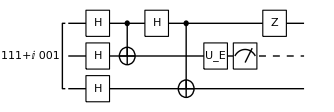

```mathematica
jj=Range[3];
ss=S[jj,None];
gg={Ket[ss->1]+I Ket[S[3]->1],
S[jj,6],
CNOT[S[1],S[2]],S[1,6],
CNOT[S[1],S[3]],
EulerRotation[{Pi/3,Pi/2,Pi/3},S[2]],
Measurement[S[2]],
S[1,3]};
qc=QuantumCircuit[Sequence@@gg]
```

```mathematica
mat1=Matrix@qc//Simplify;
mat1//Normal
mat2=Matrix[ExpressionFor@qc,ss];
mat2//Normal
mat3=Matrix@qc//Simplify;
mat3//Normal
mat1-mat2//Simplify//Normal
mat2-mat3//Simplify//Normal
{Readout[ExpressionFor[mat1,ss],S[2]],
Readout[ExpressionFor[mat2,ss],S[2]]}
```

{((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3)),-((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3)),0,0,0,0,0,0}

{((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3)),-((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3)),0,0,0,0,0,0}

{((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3)),-((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3)),0,0,0,0,0,0}

{0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0}

{0,0}

Let us collect the measurement readouts to get the statistics.

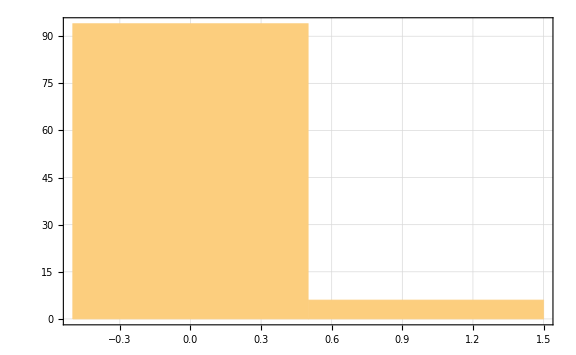

```mathematica
data1=Table[(
result=Matrix[qc];
Readout[ExpressionFor[result,ss],S[2]]
),100];
Histogram[data1]
```

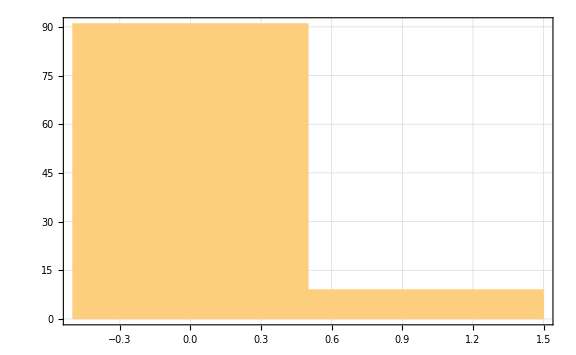

```mathematica
data2=Table[(result=ExpressionFor[qc];
Readout[result,S[2]]),100];
Histogram[data2]
```

| Related Guides
▪Quisso Package Guide

| Related Tutorials
▪Quisso: Quick Start
▪Quantum Teleportation
▪Quantum Fourier Transform
▪Quantum Fourier Transform: Semiclassical Implementation

| Related Wolfram Education Group Courses
An Elementary Introduction to the Wolfram Languagehttps://www.wolfram.com/language/elementary-introduction/
The Wolfram Language: Fast Introduction for Programmershttps://www.wolfram.com/language/fast-introduction-for-programmers/